```mathematica
ψ[z_]:= 0.015*(1+z)^2.7/(1+((1+z)/2.9)^5.6);
ψ1[z_]=0.16*Exp[3.4*z]/(Exp[3.4*z]+22)*((0.73+0.27*(1+z)^3)^0.5)/(1+z)^1.5;
omegam=0.3;
omegalambda=0.7;
H0=2.2685*10^-18*1/(3.171*10^-8);
ρ[z_]:=(1-0.27)*NIntegrate[ψ[p]/((1+p)*H0*(omegam*(1+p)^3+omegalambda)^0.5),{p,z,∞}];
```

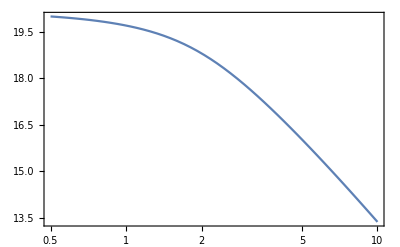

```mathematica
LogLinearPlot[Log[ρ[z]],{z,0.5,10},Frame->True]
```

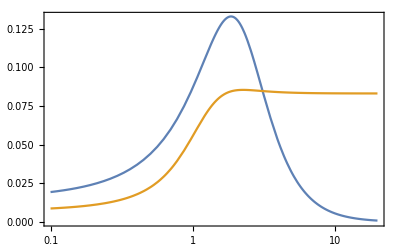

```mathematica
LogLinearPlot[{ψ[z],ψ1[z]},{z,0.1,20},Frame->True]
```

```mathematica
(*********************************************************************)
```

```mathematica
(*PBH merger rate with redshift*)

GN=6.707*10^-39;(*In GeV^-2*)
G=6.674*10^-11;(* in SI*)
```

```mathematica
H0=2.197*10^-18;(*in s^-1*)
omegadm=0.27;
t0=13.7*10^9*3.171*10^7;(*in s*)


npbh[mpbh_,fpbh_]:=(3*H0^2)/(8*π*G)*(fpbh*omegadm)/(mpbh*10^-3);(*in m^-3*)
```

```mathematica
ymax[mpbh_,fpbh_]:=((4*π)/3*npbh[mpbh,fpbh])^(-1/3);(*mpbh in g*)(*in m*)
```

```mathematica
T[mpbh_,fpbh_]:=3/170*1/((GN*mpbh*5.62*10^23)^3)*(3/(4*π*(1+3450)*fpbh)*ymax[mpbh,fpbh]*5.06*10^15)^4*(1.52*10^24)^-1;(*mpbh in g*)(*in s*)
tc[mpbh_,fpbh_]:=T[mpbh,fpbh]*((4*π*fpbh)/3)^(37/3);
```

```mathematica
R[mpbh_,fpbh_]:=3/58*npbh[mpbh,fpbh]*(t0/T[mpbh,fpbh])^(3/8)*1/t0*If[t0<tc[mpbh,fpbh],(1/(t0/T[mpbh,fpbh])^(75/296)-1),(1/(((4*π*fpbh)/3)^(25/8)*(t0/tc[mpbh,fpbh])^(25/56))-1)]*(3.24*10^-26)^-3*(3.171*10^-8)^-1;(*in Gpc^-3 yr^-1*)
```

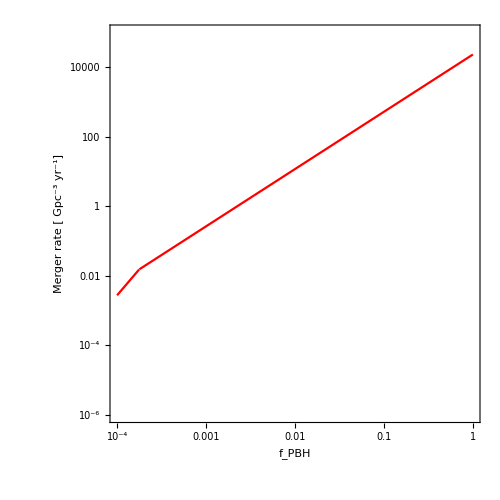

```mathematica
LogLogPlot[R[30*2*10^33,x],{x,10^-4,1},Frame->True,AspectRatio->1,ImageSize->500,FrameStyle->Directive[14, "Times",Black],PlotRange->{{10^-4,1},{10^-6,10^5}},FrameLabel->{Style["f_PBH",FontSize->20,Bold],Style["Merger rate [ Gpc^-3 yr^-1]",FontSize->20,Bold]},PlotStyle->Red]
```

```mathematica
omegalambda=(1-omegam-omegar);
omegam=0.307;
omegar=9.061*10^-5;
```

```mathematica
t[z_]:=1/H0*NIntegrate[1/((1+p)*(omegalambda+omegam*(1+p)^3+omegar(1+p)^4)^0.5),{p,z,∞}];
```

```mathematica
R2[mpbh_,fpbh_,z_]:=3/58*npbh[mpbh,fpbh]*(t[z]/T[mpbh,fpbh])^(3/8)*1/t[z]*If[t[z]<tc[mpbh,fpbh],1/(t[z]/T[mpbh,fpbh])^(75/296)-1,1/(((4*π*fpbh)/3)^(25/8)*(t[z]/tc[mpbh,fpbh])^(25/56))-1]*(3.24*10^-26)^-3*(3.17*10^-8)^-1;(*in Gpc^-3 yr^-1*)
```

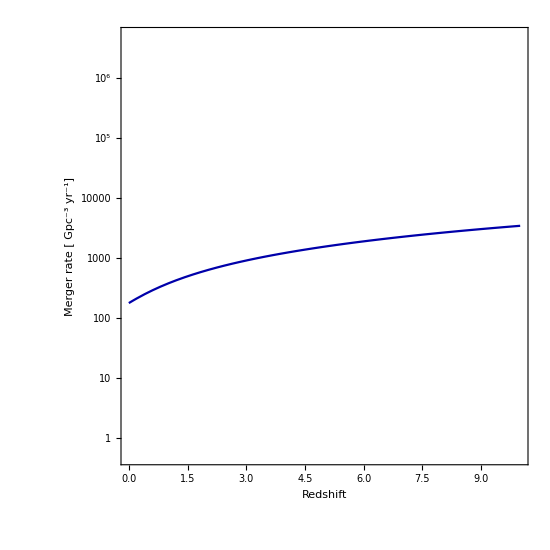

```mathematica
LogPlot[R2[2*10^33,0.01,z],{z,0,10},Frame->True,AspectRatio->1,ImageSize->550,FrameStyle->Directive[18, "Times",Black,Thickness[0.003]],FrameTicksStyle->24,PlotRange->{{0,10},{0.5,5*10^6}},FrameLabel->{Style["Redshift",FontSize->28],Style["Merger rate [ Gpc^-3 yr^-1]",FontSize->28]},PlotStyle->Darker[Blue],ImagePadding->{{Automatic,20},{100,20}}]
```

```mathematica
42.5*10^3*(10.31*π)/(180*60*60)(*in kpc*)
```

2.12433

```mathematica
42.5*10^3*(0.05*π)/(180*60*60)(*in kpc*)
```

0.0103023

```mathematica
(**************************************************************************************************)
```

```mathematica
(*NFW*)
```

```mathematica
c200=7.52;
```

```mathematica
ρc=1.05*10^-5*0.674^2;(*in GeV/cm^3*)
```

```mathematica
ρ0=200*ρc*c200*(1+c200)^2
```

0.520758

```mathematica
FindRoot[NIntegrate[(ρ0*(3.086*10^21)^3)/(r/(r200/c200)*(1+r/(r200/c200))^2)*4*π*r^2,{r,0,r200}]==1.94*10^12*2*10^33*5.62*10^23,{r200,100}]//Quiet
```

{r200→156.422}

```mathematica
rs=156.422/c200(*in kpc*)
```

20.8008

```mathematica
0.52/(0.01/rs*(1+0.01/rs)^2)(*DM density at GeV/cm^3*)
```

1080.6

```mathematica
0.52/(5/rs*(1+5/rs)^2)
```

1.40607

```mathematica
0.52/(2.12/rs*(1+2.12/rs)^2)(*DM density at GeV/cm^3*)
```

4.20192

```mathematica
0.52/(5/rs*(1+5/rs)^2)
```

1.40607

```mathematica
(*FindRoot[NIntegrate[(ρ0*(3.086*10^21)^3)/(r/rs*(1+r/rs)^2)*4*π*r^2,{r,0,rmax}]==1.94*10^12*2*10^33*5.62*10^23,{rmax,100}]//Quiet*)
```

```mathematica
(**************************************************************************************************)
```

```mathematica
(*NS merger rate with redshift*)(*1501.01115*)
```

```mathematica
t0=3*10^9;(*in yr*)
τ=0.3;
```

```mathematica
tage=13.7*10^9;(*in yr*)
```

```mathematica
t[z_]:=NIntegrate[(9.78*(0.71)^-1*10^9)/((1+p)*(0.73+0.27*(1+p)^3)^0.5),{p,z,∞}];(*in yr*)
```

```mathematica
t[30]
```

1.0239×10^8

```mathematica
ψ[z_]:=1/((t[z]-0.2*10^9)*(2*π*τ^2)^0.5)*Exp[(-Log[(t[z]-0.2*10^9)/t0]^2)/(2*τ^2)];(*in yr^-1*)
```

```mathematica
(*LogLogPlot[ψ[z],{z,0.1,50},Frame->True]*)
```

```mathematica
R[z_]:=NIntegrate[10^18*0.086*Exp[(-Log[m/0.22]^2)/(2*0.57^2)],{m,8,20}]*ψ[z];(*in Mpc^-3 yr^-1*)
```

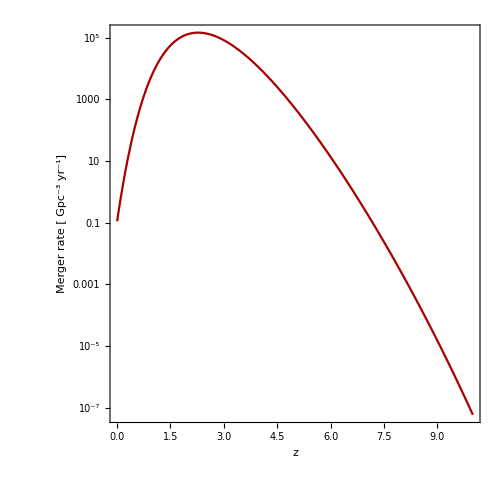

```mathematica
LogPlot[10^9*0.002*R[z],{z,0,10},Frame->True,AspectRatio->1,ImageSize->500,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [ Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Darker[Red]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data10=Import["data.dat","Table"];
```

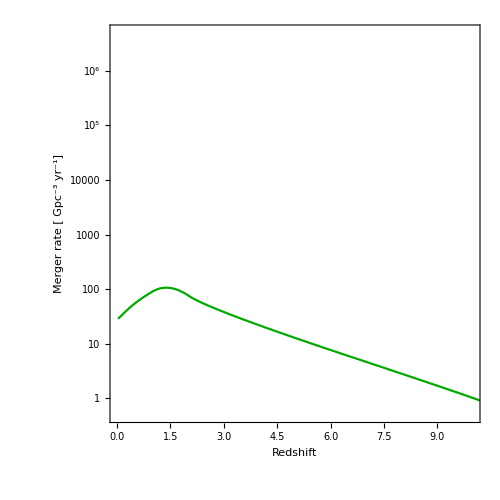

```mathematica
ListLogPlot[{Table[{data10[[i,1]],data10[[i,2]]},{i,Length[data10]}]},Frame->True,AspectRatio->1,ImageSize->500,FrameTicksStyle->16,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],PlotRange->{{0,10},{0.5,5*10^6}},Joined->True,InterpolationOrder->2,FrameLabel->{Style["Redshift",FontSize->20],Style["Merger rate [ Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Darker[Green]]
```

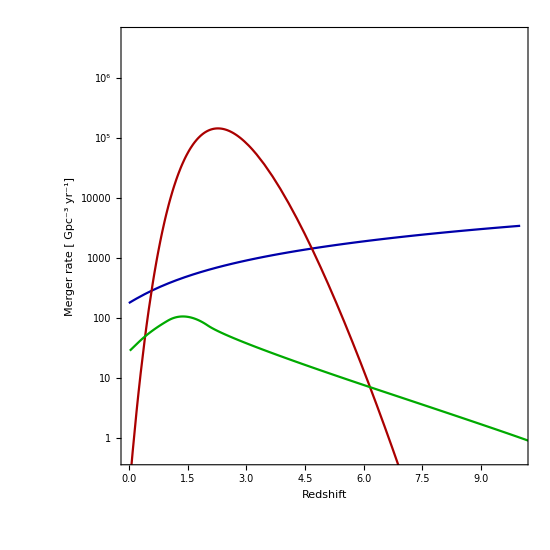

```mathematica
p=Show[-Graphics-,-Graphics-,-Graphics-,Graphics[Rotate[Text[Style["PBH-PBH merger",Blue,FontSize->20],Scaled[{0.75,0.46}]],0 Degree]],Graphics[Rotate[Text[Style["TBH-TBH merger",Red,FontSize->20],Scaled[{0.52,0.75}]],0 Degree]],Graphics[Rotate[Text[Style["TBH-NS merger",Darker[Green],FontSize->20],Scaled[{0.8,0.2}]],0 Degree]]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["merger_rate.pdf",p];
```

```mathematica
(*NS distribution with DM density Sertore et al*)
```

```mathematica
R0=4.5;(*in kpc*)
```

```mathematica
nns[r_]:=9752*r/R0*Exp[-r/R0];(*in kpc^-3*)
nnsv2[r_]:=5811*(r/8.5)^2*Exp[(-3.53*(r-8.5))/8.5];(*in kpc^-3*)
```

```mathematica
Integrate[nns[r]*4*π*r^2,{r,0,150}]
```

6.70027×10^7

```mathematica
Integrate[nnsv2[r]*4*π*r^2,{r,0,150}]
```

6.70062×10^7

```mathematica
rs=20.8008;(*in kpc*)
ρ0=0.52;(*in GeV/cm^3*)
```

```mathematica
Solve[x*(1+x)^2==a,x]
```

{{x→1/3 (-2+2^(1/3)/((2+27 a+3 √3 √(4 a+27 a^2))^(1/3))+((2+27 a+3 √3 √(4 a+27 a^2))^(1/3))/2^(1/3))},{x→-2/3-(1+ⅈ √3)/(3 2^(2/3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))-((1-ⅈ √3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))/(6 2^(1/3))},{x→-2/3-(1-ⅈ √3)/(3 2^(2/3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))-((1+ⅈ √3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))/(6 2^(1/3))}}

```mathematica
r[ρ_]:=rs/3* (-2+2^(1/3)/((2+27*ρ0/ρ+3 √3 √(4*ρ0/ρ+27*(ρ0/ρ)^2))^(1/3))+((2+27*ρ0/ρ+3 √3 √(4*ρ0/ρ+27*(ρ0/ρ)^2))^(1/3))/2^(1/3));(*r in kpc, input ρ in GeV cm^-3*)
```

```mathematica
r[1]
```

6.34905

```mathematica
myticks={{{{10^-5,"10^-5",{0.020,0}},{10^-4,"",{0.010,0}},{0.001,"10^-3",{0.020,0}},{0.01,"",{0.010,0}},{0.1,"0.1",{0.020,0}},{1,"",{0.010,0}},{10,"10",{0.020,0}},{10^2,"",{0.010,0}},{10^3,"10^3",{0.020,0}},{10^4,"",{0.010,0}},{10^5,"10^5",{0.020,0}}},{{10^-5,"",{0.020,0}},{10^-4,"",{0.010,0}},{0.001,"",{0.020,0}},{0.01,"",{0.010,0}},{0.1,"",{0.020,0}},{1,"",{0.010,0}},{10,"",{0.020,0}},{10^2,"",{0.010,0}},{10^3,"",{0.020,0}},{10^4,"",{0.010,0}},{10^5,"",{0.020,0}}}},{{{0.001,"0.001",{0.020,0}},{0.01,"",{0.010,0}},{0.1,"",{0.010,0}},{1,"1",{0.020,0}},{10,"",{0.010,0}},{100,"",{0.010,0}},{10^3,"10^3",{0.020,0}},{10^4,"",{0.010,0}},{10^5,"",{0.010,0}},{10^6,"10^6",{0.020,0}}},{{0.0032,"100",{0.020,0}},{0.493,"10",{0.020,0}},{9.840,"1",{0.020,0}},{107,"0.1",{0.020,0}},{1080,"0.01",{0.020,0}},{1.08*10^4,"0.001",{0.020,0}},{1.08*10^5,"10^-4",{0.020,0}}}}};
```

```mathematica
nns2[ρ_]:=9752*r[ρ]/R0*Exp[(-r[ρ])/R0];(*in kpc^-3*)
nns2v2[ρ_]:=5811*(r[ρ]/8.5)^2*Exp[(-3.53*(r[ρ]-8.5))/8.5];(*in kpc^-3*)
```

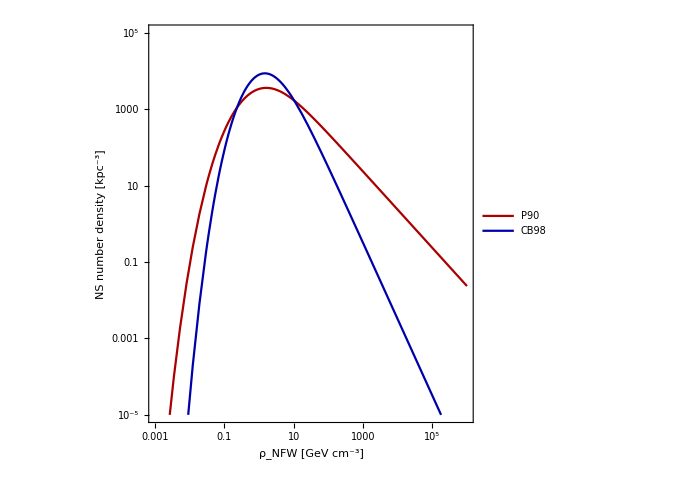

```mathematica
p=Show[LogLogPlot[nns2[ρ],{ρ,0.001,10^6},Frame->True,AspectRatio->1,ImageSize->500,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],PlotRange->{Automatic,{10^-5,10^5}},FrameLabel->{{Style["NS number density [kpc^-3]",FontSize->20],None},{Style["ρ_NFW [GeV cm^-3]",FontSize->20],Style["r [kpc]",FontSize->20]}},PlotStyle->Darker[Red],FrameTicks->myticks,PlotLegends->Placed[{Style["P90",FontSize->16]},{0.82,0.9}]],LogLogPlot[nns2v2[ρ],{ρ,0.001,10^6},Frame->True,AspectRatio->1,ImageSize->500,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],PlotRange->{Automatic,{10^-5,10^5}},FrameLabel->{{Style["NS number density [kpc^-3]",FontSize->20],None},{Style["ρ_NFW [GeV cm^-3]",FontSize->20],Style["r [kpc]",FontSize->20]}},PlotStyle->Darker[Blue],FrameTicks->myticks,PlotLegends->Placed[{Style["CB98",FontSize->16]},{0.835,0.83}]]]
```

```mathematica
Integrate[nns[r]*4*π*r^2,{r,0.001,100}]
```

6.70027×10^7

```mathematica
func[ρ_]:=D[r[p],p]/.{p->ρ};
```

```mathematica
NIntegrate[nns2[ρ]*4*π*r[ρ]^2*func[ρ],{ρ,1.08*10^4,0.0032}]
```

6.70027×10^7

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["NS_DM density.pdf",p];
```

```mathematica
(*NS distribution with DM density Taani et al*)
```

```mathematica
1.0684*Integrate[R/4.5^2*Exp[-R/4.5],{R,0,20}](*probability distribution function integrates to 1*)
```

1.00009

```mathematica
n1[r_]:=2308*1.0684*Integrate[R/4.5^2*Exp[-R/4.5],{R,0,r}];
```

```mathematica
Integrate[n1[r]*4*π*r^2,{r,0,20}]
```

6.70181×10^7

```mathematica
rs=20.8008;(*in kpc*)
ρ0=0.52;(*in GeV/cm^3*)
```

```mathematica
Solve[x*(1+x)^2==a,x]
```

{{x→1/3 (-2+2^(1/3)/((2+27 a+3 √3 √(4 a+27 a^2))^(1/3))+((2+27 a+3 √3 √(4 a+27 a^2))^(1/3))/2^(1/3))},{x→-2/3-(1+ⅈ √3)/(3 2^(2/3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))-((1-ⅈ √3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))/(6 2^(1/3))},{x→-2/3-(1-ⅈ √3)/(3 2^(2/3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))-((1+ⅈ √3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))/(6 2^(1/3))}}

```mathematica
r[ρ_]:=rs/3* (-2+2^(1/3)/((2+27*ρ0/ρ+3 √3 √(4*ρ0/ρ+27*(ρ0/ρ)^2))^(1/3))+((2+27*ρ0/ρ+3 √3 √(4*ρ0/ρ+27*(ρ0/ρ)^2))^(1/3))/2^(1/3));(*r in kpc, input ρ in GeV cm^-3*)
```

```mathematica
n1[r]
```

2465.87 (1.+ⅇ^(-0.222222 r) (-1.-0.222222 r))

```mathematica
n1f[ρ_]:=2465.87*(1+Exp[(-r[ρ])/4.5]*(-1-r[ρ]/4.5));
```

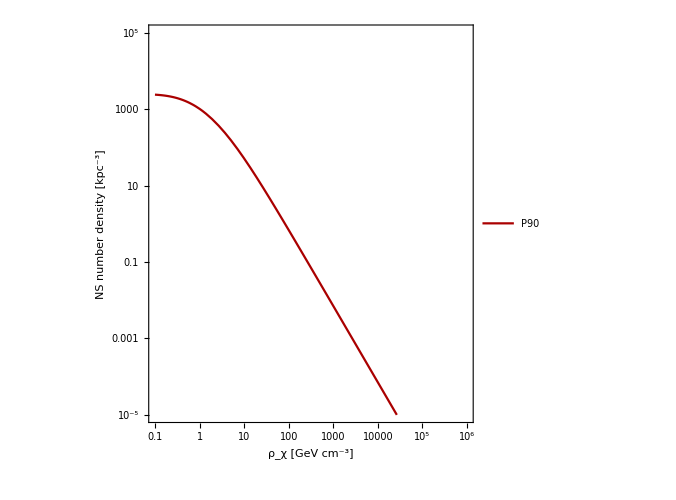

```mathematica
LogLogPlot[n1f[ρ],{ρ,0.1,10^6},Frame->True,AspectRatio->1,ImageSize->500,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],PlotRange->{Automatic,{10^-5,10^5}},FrameLabel->{{Style["NS number density [kpc^-3]",FontSize->20],None},{Style["ρ_χ [GeV cm^-3]",FontSize->20],Style["r [kpc]",FontSize->20]}},PlotStyle->Darker[Red],FrameTicks->myticks,PlotLegends->Placed[{Style["P90",FontSize->16]},{0.82,0.9}]]
```

```mathematica
(*NS distribution with DM density Safdi et al*)
```

```mathematica
n1[r_]:=(4*10^8)/(4*π*5*1)*Exp[-r^2/(2*5^2)]+(6*10^8)/(2*π)*0.6/r*1/(0.6+r)^3+(1.7*7*10^5)/(4*π*(0.012)^3)*(r/0.012)^-1.3*(1+r/0.012)^-2.7;(*in kpc^-3*)
```

```mathematica
Integrate[n1[r]*4*π*r^2,{r,0.001,5}]
```

2.96994×10^9

```mathematica
Integrate[n1[r]*4*π*r^2,{r,0.001,0.002}]
```

21631.6

```mathematica
Integrate[n1[r]*4*π*r^2,{r,0.01,0.02}]
```

594910.

```mathematica
Integrate[n1[r]*4*π*r^2,{r,0.1,0.2}]
```

2.54983×10^7

```mathematica
Integrate[n1[r]*4*π*r^2,{r,1,2}]
```

2.97693×10^8

```mathematica
rs=20.8008;(*in kpc*)
ρ0=0.4;(*in GeV/cm^3*)
```

```mathematica
Solve[x*(1+x)^2==a,x]
```

{{x→1/3 (-2+2^(1/3)/((2+27 a+3 √3 √(4 a+27 a^2))^(1/3))+((2+27 a+3 √3 √(4 a+27 a^2))^(1/3))/2^(1/3))},{x→-2/3-(1+ⅈ √3)/(3 2^(2/3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))-((1-ⅈ √3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))/(6 2^(1/3))},{x→-2/3-(1-ⅈ √3)/(3 2^(2/3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))-((1+ⅈ √3) (2+27 a+3 √3 √(4 a+27 a^2))^(1/3))/(6 2^(1/3))}}

```mathematica
r[ρ_]:=rs/3* (-2+2^(1/3)/((2+27*ρ0/ρ+3 √3 √(4*ρ0/ρ+27*(ρ0/ρ)^2))^(1/3))+((2+27*ρ0/ρ+3 √3 √(4*ρ0/ρ+27*(ρ0/ρ)^2))^(1/3))/2^(1/3));(*r in kpc, input ρ in GeV cm^-3*)
```

```mathematica
r[10^4]
```

0.000831965

```mathematica
(*n1f[ρ_]:=(4*10^8)/(4*π*5*1)*Exp[(-r[ρ]^2)/(2*5^2)]+(6*10^8)/(2*π)*0.6/r[ρ]*1/(0.6+r[ρ])^3;*)
```

```mathematica
(*LogLogPlot[n1f[ρ],{ρ,0.1,10^6},Frame->True,AspectRatio->1,ImageSize->500,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{{Style["NS number density [kpc^-3]",FontSize->20],None},{Style["ρ_χ [GeV cm^-3]",FontSize->20],Style["r [kpc]",FontSize->20]}},PlotStyle->Darker[Red]]*)
```

```mathematica
myticks={{{{10^3,"10^3",{0.020,0}},{2*10^3,"",{0.010,0}},{4*10^3,"",{0.010,0}},{6*10^3,"",{0.010,0}},{8*10^3,"",{0.010,0}},{10^4,"",{0.020,0}},{2*10^4,"",{0.010,0}},{4*10^4,"",{0.010,0}},{6*10^4,"",{0.010,0}},{8*10^4,"",{0.010,0}},{10^5,"10^5",{0.020,0}},{2*10^5,"",{0.010,0}},{4*10^5,"",{0.010,0}},{6*10^5,"",{0.010,0}},{8*10^5,"",{0.010,0}},{10^6,"",{0.020,0}},{2*10^6,"",{0.010,0}},{4*10^6,"",{0.010,0}},{6*10^6,"",{0.010,0}},{8*10^6,"",{0.010,0}},{10^7,"10^7",{0.020,0}},{2*10^7,"",{0.010,0}},{4*10^7,"",{0.010,0}},{6*10^7,"",{0.010,0}},{8*10^7,"",{0.010,0}},{10^8,"",{0.020,0}},{2*10^8,"",{0.010,0}},{4*10^8,"",{0.010,0}},{6*10^8,"",{0.010,0}},{6*10^8,"",{0.010,0}},{10^9,"10^9",{0.020,0}},{2*10^9,"",{0.010,0}},{4*10^9,"",{0.010,0}},{6*10^9,"",{0.010,0}},{8*10^9,"",{0.010,0}},{10^10,"",{0.020,0}},{2*10^10,"",{0.010,0}},{4*10^10,"",{0.010,0}},{6*10^10,"",{0.010,0}},{8*10^10,"",{0.010,0}},{10^11,"10^11",{0.020,0}},{2*10^11,"",{0.010,0}},{4*10^11,"",{0.010,0}},{6*10^11,"",{0.010,0}},{8*10^11,"",{0.010,0}},{10^12,"",{0.020,0}},{2*10^12,"",{0.010,0}},{4*10^12,"",{0.010,0}},{6*10^12,"",{0.010,0}},{8*10^12,"",{0.010,0}},{10^13,"10^13",{0.020,0}}},{{10^3,"",{0.020,0}},{2*10^3,"",{0.010,0}},{4*10^3,"",{0.010,0}},{6*10^3,"",{0.010,0}},{8*10^3,"",{0.010,0}},{10^4,"",{0.020,0}},{2*10^4,"",{0.010,0}},{4*10^4,"",{0.010,0}},{6*10^4,"",{0.010,0}},{8*10^4,"",{0.010,0}},{10^5,"",{0.020,0}},{2*10^5,"",{0.010,0}},{4*10^5,"",{0.010,0}},{6*10^5,"",{0.010,0}},{8*10^5,"",{0.010,0}},{10^6,"",{0.020,0}},{2*10^6,"",{0.010,0}},{4*10^6,"",{0.010,0}},{6*10^6,"",{0.010,0}},{8*10^6,"",{0.010,0}},{10^7,"",{0.020,0}},{2*10^7,"",{0.010,0}},{4*10^7,"",{0.010,0}},{6*10^7,"",{0.010,0}},{8*10^7,"",{0.010,0}},{10^8,"",{0.020,0}},{2*10^8,"",{0.010,0}},{4*10^8,"",{0.010,0}},{6*10^8,"",{0.010,0}},{6*10^8,"",{0.010,0}},{10^9,"",{0.020,0}},{2*10^9,"",{0.010,0}},{4*10^9,"",{0.010,0}},{6*10^9,"",{0.010,0}},{8*10^9,"",{0.010,0}},{10^10,"",{0.020,0}},{2*10^10,"",{0.010,0}},{4*10^10,"",{0.010,0}},{6*10^10,"",{0.010,0}},{8*10^10,"",{0.010,0}},{10^11,"",{0.020,0}},{2*10^11,"",{0.010,0}},{4*10^11,"",{0.010,0}},{6*10^11,"",{0.010,0}},{8*10^11,"",{0.010,0}},{10^12,"",{0.020,0}},{2*10^12,"",{0.010,0}},{4*10^12,"",{0.010,0}},{6*10^12,"",{0.010,0}},{8*10^12,"",{0.010,0}},{10^13,"",{0.020,0}}}},{{{0.0001,"10^-4",{0.020,0}},{2*10^-4,"",{0.010,0}},{3*10^-4,"",{0.010,0}},{4*10^-4,"",{0.010,0}},{5*10^-4,"",{0.010,0}},{6*10^-4,"",{0.010,0}},{7*10^-4,"",{0.010,0}},{8*10^-4,"",{0.010,0}},{9*10^-4,"",{0.010,0}},{0.001,"0.001",{0.020,0}},{2*10^-3,"",{0.010,0}},{3*10^-3,"",{0.010,0}},{4*10^-3,"",{0.010,0}},{5*10^-3,"",{0.010,0}},{6*10^-3,"",{0.010,0}},{7*10^-3,"",{0.010,0}},{8*10^-3,"",{0.010,0}},{9*10^-3,"",{0.010,0}},{0.01,"0.01",{0.020,0}},{0.02,"",{0.010,0}},{0.03,"",{0.010,0}},{0.04,"",{0.010,0}},{0.05,"",{0.010,0}},{0.06,"",{0.010,0}},{0.07,"",{0.010,0}},{0.08,"",{0.010,0}},{0.09,"",{0.010,0}},{0.1,"0.1",{0.020,0}},{0.2,"",{0.010,0}},{0.3,"",{0.010,0}},{0.4,"",{0.010,0}},{0.5,"",{0.010,0}},{0.6,"",{0.010,0}},{0.7,"",{0.010,0}},{0.8,"",{0.010,0}},{0.9,"",{0.010,0}},{1,"1",{0.020,0}},{2,"",{0.010,0}},{3,"",{0.010,0}},{4,"",{0.010,0}},{5,"",{0.010,0}},{6,"",{0.010,0}},{7,"",{0.010,0}},{8,"",{0.010,0}},{9,"",{0.010,0}},{10,"10",{0.020,0}},{20,"",{0.010,0}},{100,"",{0.010,0}},{10^3,"10^3",{0.020,0}},{10^4,"",{0.020,0}},{10^5,"",{0.020,0}},{10^6,"10^6",{0.020,0}}},{{20.8008,"0.1",{0.020,0}},{5.28887,"1",{0.020,0}},{0.773444,"10",{0.020,0}},{0.0825467,"100",{0.020,0}},{0.00831367,"1000",{0.020,0}},{0.000831965,"10^4",{0.020,0}},{1.08*10^5,"10^-4",{0.020,0}}}}};
```

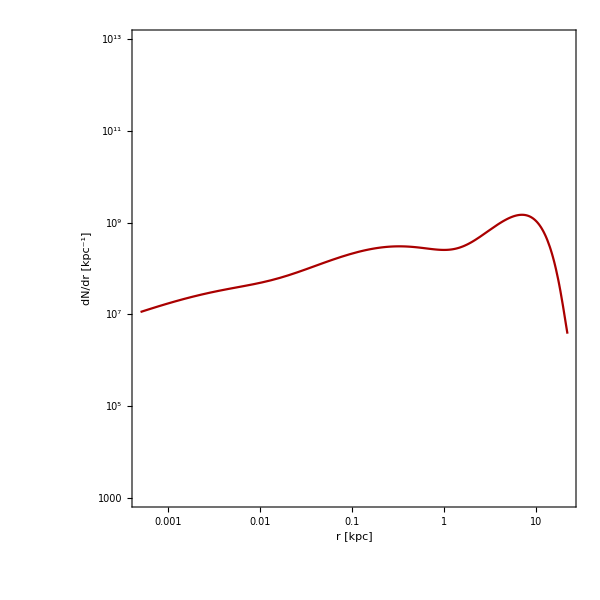

```mathematica
p=LogLogPlot[{n1[r]*r^2*4*π},{r,0.0005,22},Frame->True,AspectRatio->1,ImageSize->600,FrameStyle->Directive[18, "Times",Black,Thickness[0.003]],FrameTicksStyle->24,FrameLabel->{{Style["dN/dr [kpc^-1]",FontSize->28],None},{Style["r [kpc]",FontSize->28],Style["ρ_NFW [GeV cm^-3]",FontSize->28]}},PlotStyle->Darker[Red],FrameTicks->myticks,PlotRange->{Automatic,{10^3,10^13}},ImageMargins->0]
```

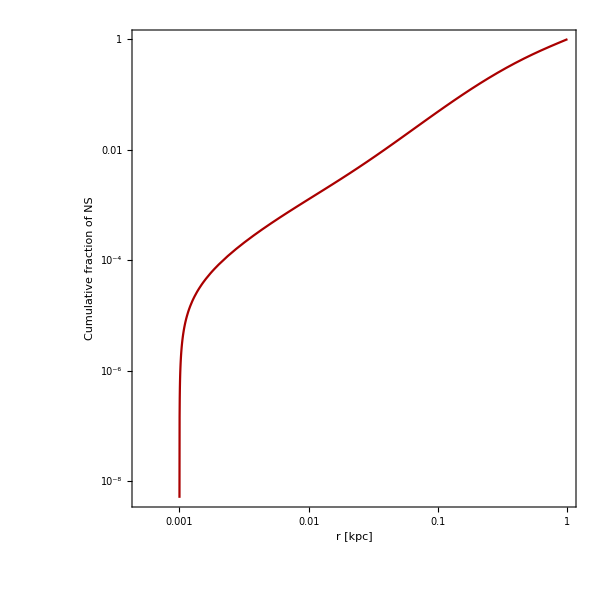

```mathematica
LogLogPlot[{NIntegrate[n1[r]*4*π*r^2,{r,0.001,r1}]/NIntegrate[n1[r]*4*π*r^2,{r,0.001,1}]},{r1,0.0005,1},Frame->True,AspectRatio->1,ImageSize->600,FrameStyle->Directive[18, "Times",Black,Thickness[0.003]],FrameTicksStyle->24,FrameLabel->{{Style["Cumulative fraction of NS",FontSize->28],None},{Style["r [kpc]",FontSize->28],Style["ρ_NFW [GeV cm^-3]",FontSize->28]}},PlotStyle->Darker[Red]]
```

```mathematica
NIntegrate[n1[r]*4*π*r^2,{r,0.1,1}]/NIntegrate[n1[r]*4*π*r^2,{r,0.001,1}]*100
```

95.0886

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["NS_DM_density.pdf",p];
```

```mathematica
(H(t)=1/(a(t))*da/dt)--------->(dt/dz= -1/(H(z)*(1+z)))
```